### Origin of Self-Replication in 1D CA model

#### Key idea:

Random “soup” environment, unlikely event of two blue cells next to each other sets a self-replication chain to go off.

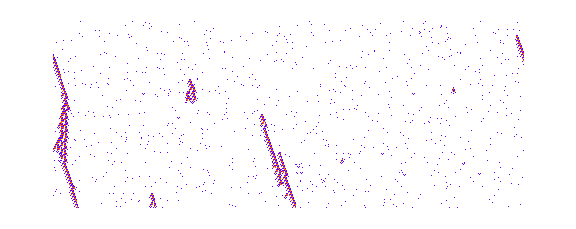

```mathematica
Module[{tmin = 0, tmax = 200, nperts = 1000, xmin = 0, xmax = 500},
SeedRandom[111141];coords=Transpose@{RandomInteger[{tmin + 1,tmax},nperts],RandomInteger[{xmin +1,xmax},nperts]}->2;
ArrayPlot[#,ColorRules->{0->GrayLevel[1],1->Hue[0.06,1,1],2->Hue[0.73,1,1],3->Hue[0.14,0.81,0.99]}, ImageSize->Large]&[ResourceFunction["PerturbedCellularAutomaton"][{3019941697641,3,1},{0},{{tmin + 1, tmax},{-1,1}*Ceiling[xmax /2]},coords,"ReturnPerturbations"->False]]]
```

#### Nearby rules are also candidates

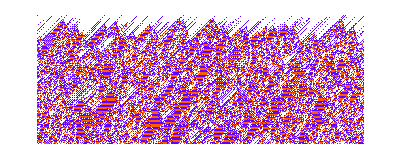
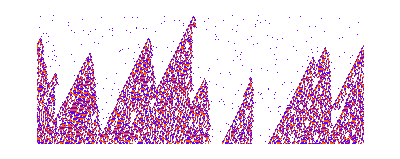
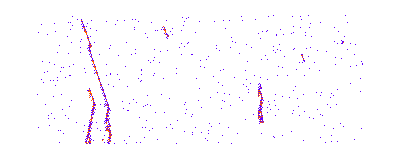
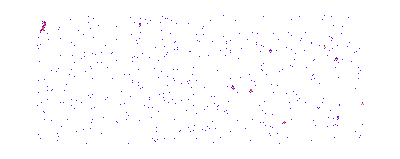
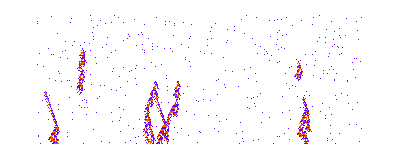
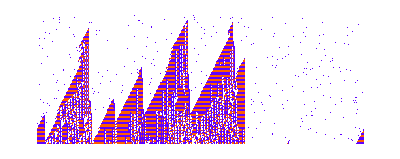
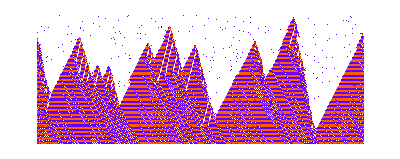
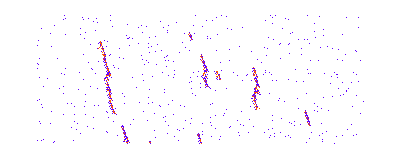
{-Graphics-{3019941697659,3,1},-Graphics-{3019941697695,3,1},-Graphics-{3019941697479,3,1},-Graphics-{3019927348734,3,1},-Graphics-{3051322757250,3,1},-Graphics-{3302371234122,3,1},-Graphics-{4714518916527,3,1},-Graphics-{3019683417315,3,1},-Graphics-{3019683417315,3,1},-Graphics-{2831655339987,3,1},-Graphics-{3867230307084,3,1},-Graphics-{3019938508995,3,1},-Graphics-{3019941697635,3,1},-Graphics-{3867230307084,3,1},-Graphics-{3019941874788,3,1},-Graphics-{3019898650920,3,1},-Graphics-{3019941697695,3,1},-Graphics-{3040862404047,3,1},-Graphics-{3030402050844,3,1},-Graphics-{3019941691080,3,1},-Graphics-{3019941697668,3,1},-Graphics-{3019941677958,3,1},-Graphics-{3019932131703,3,1},-Graphics-{2925798518814,3,1},-Graphics-{3019912999827,3,1},-Graphics-{3019683417315,3,1},-Graphics-{3019941697479,3,1},-Graphics-{3016454913240,3,1},-Graphics-{3019936914672,3,1},-Graphics-{2925798518814,3,1},-Graphics-{3019941815739,3,1},-Graphics-{2737512161160,3,1},-Graphics-{3019941704202,3,1},-Graphics-{3019941697560,3,1},-Graphics-{3019941698370,3,1},-Graphics-{478075869312,3,1},-Graphics-{3019942051935,3,1},-Graphics-{3019940103318,3,1},-Graphics-{3012968128839,3,1},-Graphics-{3019941699099,3,1},-Graphics-{2925798518814,3,1},-Graphics-{3019941699099,3,1},-Graphics-{3022266220575,3,1},-Graphics-{3019942051935,3,1},-Graphics-{3019941874788,3,1},-Graphics-{3019941658275,3,1},-Graphics-{3019941166200,3,1},-Graphics-{3302371234122,3,1},-Graphics-{3019855604199,3,1},-Graphics-{3019938508995,3,1}}

```mathematica
Module[{tmin = 0, tmax = 200, nperts = 1000, xmin = 0, xmax = 500, muru},
Table[
SeedRandom[111151+i];muru = {{"[◼]", "RandomRuleMutation"}}[{3019941697641,3,1}];coords=Transpose@{RandomInteger[{tmin + 1,tmax},nperts],RandomInteger[{xmin +1,xmax},nperts]}->2;
Labeled[ArrayPlot[#,ColorRules->{0->GrayLevel[1],1->Hue[0.06,1,1],2->Hue[0.73,1,1],3->Hue[0.14,0.81,0.99]}]&[ResourceFunction["PerturbedCellularAutomaton"][muru,{0},{{tmin + 1, tmax},{-1,1}*Ceiling[xmax /2]},coords,"ReturnPerturbations"->False]], muru],  {i, 50}]]
```